```mathematica
PartitionTypeLattice3[form_]:=Block[{vars,set, com, result},
vars=ListofVars[form];
set=Map[SymbolToSets,vars];
com=Subsets[set,{2}];
result={};
Table[
If[IsTypeRefinement[pair[[1]],pair[[2]]],
AppendTo[result,DirectedEdge[pair[[1]],pair[[2]]]],
If[IsTypeRefinement[pair[[2]],pair[[1]]],
AppendTo[result,DirectedEdge[pair[[2]],pair[[1]]]]
]
]
,
{pair,com}
];
Graph[
set,
result,GraphLayout->"LayeredDigraphEmbedding", VertexLabels->Map[SymbolToSets[#]->Rotate[Column[{#,Style[Coefficient[form,#],Bold,Red]}, Alignment->Center],Pi/6]&,vars]
]
]
```

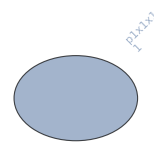

```mathematica
PartitionTypeLattice3[NullPartitionTypeFormula[allGraphs5[0,"graph"]]]
```

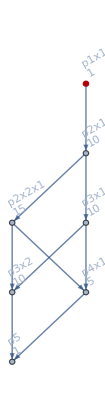
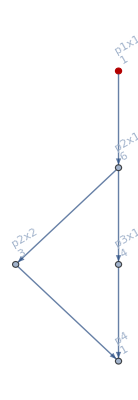
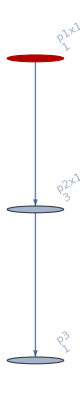
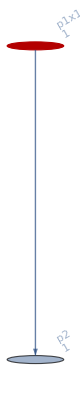
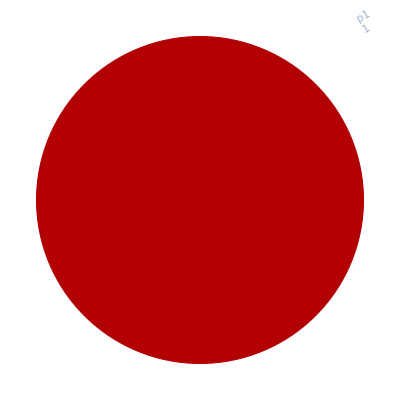
{-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-,-Graphics-→-Graphics-}

```mathematica
Table[
allGraphs5[k,"graph"]->With[{
empty=VertexList[NullPartitionTypeFormula[allGraphs5[k,"graph"]]//PartitionTypeLattice3]
},
Graph[PartitionTypeLattice3[PartitionTypeFormula[allGraphs5[k,"graph"]]],GraphHighlight->empty]
]
,
{k,allGraphs5NullAtomKeys}
]
```